## Damped Pendulum — Coordinates and Graphics

## Done in class, February 7, 2025

This is the sixth notebook for you to finish in-class.

### Forced Oscillation

#### Force and Acceleration

```mathematica
gravity = 9.80665; (* the value of gravity in units of meters / seconds-squared *)
length=0.24840; (* A pendulum whose length is 9.7795 inches converted to meters  *)
(* The natural frequency of such a pendulum provided the swings are not large: *)
omega0=Sqrt[gravity/length];
gamma=0.03; (* A real pendulum swinging in air typically has a small gamma. *)
period = 2Pi/omega0; (* The length was chosen so that the period is 1 second. To be *)
(* precise, 2 Pi / omega0 = 0.999989, and 2 Pi / Sqrt[omega0^2-gamma^2] = 1.000000. *)
α[t_, theta_, omega_]:=-omega0^2 Sin[theta]-2 gamma omega;
```

#### Simulation Parameters

```mathematica
tInitial = 0.0;
tFinal = 50.0; 
steps =200000;
deltaT = (tFinal - tInitial)/steps;
```

#### Initial Angle and Angular Velocity

Let’s let the pendulum be initially held still at 10° and gently released:

```mathematica
thetaInitial=10 °;
omegaInitial=-gamma thetaInitial; (* gamma is small, and this is only 0.3° / second. *)
(* Putting in the small initial velocity makes the algebra work out more tidily later. *)
initialConditions={tInitial,thetaInitial,omegaInitial};
```

#### General Second-Order Runge-Kutta — Implementation

The implementation of the damped pendulum is almost the same is as the damped oscillator that you just completed. Paste in the code and figure out what needs to be changed.

```mathematica
lambda=1;
rungeKutta2[cc_]:=(
(* Extract time, angle, and angular velocity from the list *)
curTime=cc[[1]];
curAngle=cc[[2]];
curAngularVelocity=cc[[3]];
(* Compute tStar, xStar, vStar *)
tStar=curTime + lambda deltaT;
thetaStar=curAngle+curAngularVelocity lambda deltaT;
omegaStar=curAngularVelocity+α[curTime,curAngle,curAngularVelocity]lambda deltaT;
(* Implement General Second-Order Runge-Kutta *)
newTime=curTime+deltaT;
newAngularVelocity=curAngularVelocity+((1-1/(2lambda))α[curTime,curAngle,curAngularVelocity]+1/(2lambda)α[tStar,thetaStar,omegaStar])deltaT;
newAngle=curAngle+(curAngularVelocity+newAngularVelocity)deltaT/2;
(* We are keeping track of the contribution to the acceleration due to the external force *)
{newTime, newAngle, newAngularVelocity}
)
N[rungeKutta2[initialConditions]] (* Test your rungeKutta2 function. *)
(* The output just below should be {0.0025,0.174498,-0.022372} *)
```

{0.00025,0.174531,-0.00694977}

#### Displaying Oscillation

Nest the procedure, transpose the results, and produce a plot of the angle θ as a function of time:

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
times = rk2ResultsTransposed[[1]];
thetas = rk2ResultsTransposed[[2]];
thetaPlot = ListPlot[Transpose[{times,thetas}]];
(* the theoretical solution is approximately known, provided the angle remains small *)
(* let's plot the envelope of the theoretical solution *)
envelopeFunction[t_]:=thetaInitial Exp[-gamma t]
approximateTheoreticalEnvelope=Plot[{envelopeFunction[t],-envelopeFunction[t]},{t, tInitial, tFinal}];
Show[{thetaPlot,approximateTheoreticalEnvelope}]
```

-Graphics-

In the preceding plot, the theoretical solution is approximately known, provided the angle remains small, and so I added the envelope of the theoretical solution to the plot.

#### Displaying Theory

In the following plot, I have included the theoretical oscillation, not just the envelope (but the same approximation that the angle must remain small still applies):

```mathematica
approximateTheoreticalOscillationPlot=Plot[{envelopeFunction[t],-envelopeFunction[t], envelopeFunction[t]Cos[Sqrt[omega0^2-gamma^2]t]},{t, tInitial, tFinal}];
```

```mathematica
Show[{thetaPlot, approximateTheoreticalOscillationPlot}]
```

-Graphics-

#### Drawing a Pendulum with Coordinates and Graphics

To do a legible job of this, we may need to review Section 14 of EIWL3. First we need a circle whose radius is length:

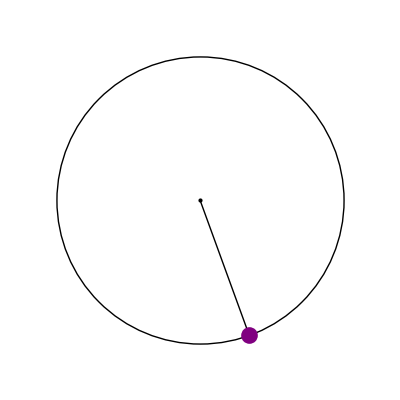

```mathematica
pendulumGraphic[angle_]:=Graphics[{
EdgeForm[Thin],White,
RegularPolygon[{0.0,0.0},0.4,4],
Black,
Circle[{0,0},length],
Point[{0,0}],
Line[{{0,0},length{ Sin[angle],- Cos[angle]}}],
PointSize[0.03], Purple,(* This directive affects any remaining items in the list *)
Point[length{ Sin[angle],- Cos[angle]}]
}]
pendulumGraphic[20°]
```

#### Animating the Graphics

It’s also nice to have an animation, arranged so that the default duration of the animation is the actual duration of the animation:

```mathematica
Animate[pendulumGraphic[thetas[[step]]],{step, 0, steps, 1}, DefaultDuration->tFinal-tInitial]
```